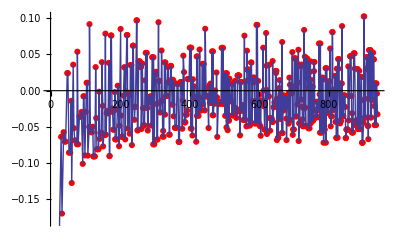

```mathematica
streamfx=OpenRead["cplxfixedpoints17april16no2"];
fxlist=ReadList[streamfx];
Close[streamfx];
stream2=OpenRead["cplxfxNrhoNloglinear20may16no1"];
list=ReadList[stream2];
Close[stream2];
data={};
For[n=0,n<600,n++;
args={};
For[a=0,a<Length[list],a++;
If[list[[a,1]]==n,args=Append[args,list[[a,3]]
] (* close Append  *)
] (* close If  *)
]; (* close Four  *)
el=Length[args];
lastdelta=args[[el]]-args[[el-1]];
mumford=lastdelta-Pi/2;
data=Append[data,{Im[betterbarryzeroslist[[n]]],mumford}]];
Show[ListPlot[data,PlotStyle->{Red,PointSize[.011]}],ListPlot[data,Joined->True]]
```

```mathematica
el
```

100